```mathematica
ResourceFunction["DarkMode"][False]
```

## Pipeline

### Processing

```mathematica
rawData = Import["/Users/erichegonzales/Downloads/01.01.2016.CHA.at.TOR.7z", "*"]
rawData = rawData[[1]]
```

```mathematica
emptyEventIdxs = Position[rawData[[3, 2]][[All, 4, 2]], {}]
```

{{33},{34},{55},{56},{57},{80},{81},{82},{83},{84},{85},{86},{89},{109},{110},{111},{126},{150},{151},{152},{153},{154},{155},{156},{187},{188},{201},{202},{213},{214},{215},{229},{230},{246},{247},{294},{452}}

```mathematica
events = Delete[rawData[[3, 2]], emptyEventIdxs];
```

```mathematica
locs = events[[All, 4, 2, All, 6]];
```

```mathematica
flatlocs = Flatten[locs, 1];
```

```mathematica
ball = DeleteDuplicates[locs[[All, All, 1]]];
```

```mathematica
ballXY = ball[[All, All, 3;;4]];
```

```mathematica
velocities = Table[EuclideanDistance[ballXY[[i]][[j]], ballXY[[i]][[j+1]]], {i,1, Length[ballXY]}, {j, 1, Length[ballXY[[i]]] - 1}];
```

```mathematica
flatballXY = Flatten[ballXY, 1];
```

```mathematica
fbp = Partition[flatballXY, 50];
```

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

```mathematica
pda = positionDuplicates[flatlocs];
pd = Select[pda,Length[#]>1&];
```

```mathematica
subPositions = Accumulate[Length/@ locs]
```

{150,1300,2450,3600,4150,4750,5350,5700,6198,6740,7282,7882,8482,9282,10082,10882,11682,12482,13282,13582,14232,14882,15532,16057,16657,17307,17782,18257,18682,19107,19582,20033,20733,21433,21833,22208,22783,23183,23808,24433,25058,25282,25506,25655,26161,26667,27241,27787,28137,28937,29731,30025,30285,30789,31293,31797,32301,32976,33575,34174,34773,35372,35971,36570,36984,37398,37812,38512,39162,39812,40038,40264,40490,40716,41041,41366,41491,41955,42318,42653,42823,43357,43891,44542,45193,45594,46019,46719,47419,47869,48469,49069,49669,50269,50519,50562,51034,51506,52206,52906,53606,54306,55006,55706,56256,56806,57344,57819,58172,58697,59332,59782,60257,60657,61107,61618,62129,62679,63068,63457,63587,63717,64216,64810,65310,65810,66310,67035,67760,68235,68810,69086,69636,70469,71302,72135,72985,73835,74685,75235,75651,76224,76797,77370,77943,78619,79110,79178,79847,80516,81185,81685,82185,82860,83335,84181,85027,85873,86171,86548,86986,87424,87930,88436,89111,89786,90261,91036,91611,92186,92613,93040,93117,93194,93891,94588,94960,95560,96160,96416,97046,97676,97917,98158,98408,98983,99645,100307,100857,101407,102182,102957,103732,104507,104907,105475,106043,106743,107443,108143,108768,109393,110018,110643,111268,111893,112518,112843,113318,113793,113993,114193,114758,115323,115620,116245,116762,117279,117904,118529,119254,119979,120779,121579,122379,123179,123979,124678,125042,125406,125495,125584,125673,125762,126562,127212,127887,128562,129037,129763,130489,131165,131867,132569,133271,133973,134623,135343,136063,136783,137503,138223,138578,138966,139354,139742,140195,140424,141059,141694,142329,143029,143568,144107,144646,145009,145372,146122,146872,147329,147786,148243,148700,149241,149816,150391,150766,151141,151460,151779,151823,151867,152467,153067,153442,154042,154642,155017,155499,155981,156463,156958,157608,158558,159083,159608,160292,160976,161110,161244,161378,161578,162284,162673,163108,163497,163764,164031,164298,164565,164897,165229,165561,165722,166260,166798,167344,167890,168208,168698,169188,169709,170308,171158,171558,172133,172645,173157,173194,173231,173268,173696,174124,174708,175292,175876,176460,176910,177735,178139,178683,178872,179061,179440,180148,180856,181306,181756,182256,182756,183131,183506,183710,183914,184118,184322,184526,184730,185149,185568,185987,186524,187061,187561,188436,189111,189786,190161,190763,191217,191671,192197,192723,193249,193775,194625,195475,195950,196570,197190,197260,197330,198005,198680,199430,200080,200530,200980,201455,201930,202697,203363,203614,203865,204116,204367,204618,205368,206118,206868,207618,207789,207935,208081,208227,208318,208908,209498,209599,209700,209825,210409,210993,211219,211445}

```mathematica
pd[[1]][[2]]
```

201

```mathematica
selectPositions = ResourceFunction["SelectPositions"]
```

```mathematica
idx1dto2d[idx1d_]:=Module[{i, j},
i = selectPositions[subPositions, idx1d< #&, 1][[1]][[1]];
j = idx1d - subPositions[[i -1]];
{i, j}
]
```

```mathematica
idx1dto2d[pd[[1]][[2]], subPositions]
```

{2,52}

```mathematica
locs[[1]][[51]]
```

{{-1,-1,34.4983,22.7963,2.57698},{1610612761,2449,12.6453,12.9098,0.},{1610612761,201960,6.46893,17.0708,0.},{1610612761,200768,34.0906,23.3762,0.},{1610612761,201942,5.78359,12.3867,0.},{1610612761,202685,23.2188,37.0152,0.},{1610612766,101107,12.6512,19.0568,0.},{1610612766,201587,9.36573,22.2898,0.},{1610612766,202689,29.6497,25.2833,0.},{1610612766,203469,16.4813,35.3397,0.},{1610612766,203798,4.55304,18.6818,0.}}

```mathematica
toDrop = Flatten[Rest/@ pd];
```

```mathematica
toDrop[[;;10]]
```

{201,1351,2501,202,1352,2502,203,1353,2503,204}

```mathematica
toDrop2d2 =  idx1dto2d/@ toDrop;
```

Part::partw: Part 1 of {} does not exist.

```mathematica
toDrop2d = idx1dto2d/@ toDrop;
```

Part::partw: Part 1 of {} does not exist.

```mathematica
toDrop2d[[-2]]
```

{415,225}

```mathematica
flatlocs[[201]] == locs[[2, 51]]
```

True

356

```mathematica
# - 1&/@ i
```

{{187}}

```mathematica
pd[[10]]
```

{10,210,1360,2510}

```mathematica
pdl = Length/@ pd;
```

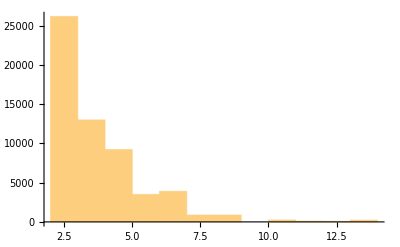

```mathematica
Histogram[pdl]
```

```mathematica
pdl3 = Select[pdl, #>3&];
```

```mathematica
Length[pdl3]
```

19021

```mathematica
Length[pd]
```

58200

```mathematica
dups[[1]]
```

{{23.4254,45.1273},{24.0045,44.6889},{24.6252,44.3009},{25.2544,43.7794},{25.7026,43.4466},{25.9734,43.1485},{26.2265,42.8935},{26.4416,42.7094},{26.7632,42.4584},{26.9761,42.2491},{27.305,42.0678},{27.519,41.7812},{27.9169,41.3719},{28.1535,41.0526},{28.5102,40.2976},{28.9097,39.8945},{29.3069,39.3563},{29.8183,38.7999},{30.3625,38.2379},{30.6542,37.7896},{30.8971,37.5838},{31.0837,37.3386},{31.3471,37.0189},{31.6587,36.6725},{31.9068,36.1895},{32.2028,35.7825},{32.2331,35.1884},{32.5812,34.6577},{32.8685,33.9739},{32.9147,33.1975},{33.0627,32.3909},{33.2495,31.5368},{33.4334,30.7201},{33.7624,30.049},{33.9449,29.2441},{34.0441,28.6021},{34.1335,27.6276},{34.2449,27.0047},{34.4641,27.5355},{34.5413,27.1658},{34.6729,26.8215},{34.6733,26.389},{34.9056,25.8818},{34.9883,25.3667},{34.9942,24.9395},{34.8783,24.8805},{34.7876,24.4632},{34.7931,23.9691},{34.7472,23.9069},{34.6865,23.6003},{34.4983,22.7963},{34.3054,22.7228},{34.0707,22.6651},{33.0044,21.2069},{31.7258,20.3533},{30.4918,19.5169},{29.3254,18.6277},{28.0784,17.4618},{27.0396,16.8649},{25.8133,15.989},{24.6888,15.1832},{23.4692,14.2248},{22.3306,13.418},{21.1972,12.627},{20.0708,11.8402},{18.9632,10.8998},{17.8078,10.1752},{16.6812,9.38974},{16.056,8.78516},{16.4058,8.76333},{16.7526,8.81312},{17.2034,8.97574},{17.5948,9.16468},{17.8235,9.70086},{18.1367,10.0058},{18.5271,10.3715},{18.6747,10.5442},{18.9131,10.4436},{18.9084,10.4993},{18.8945,10.6577},{18.8715,10.9058},{18.8397,11.2308},{18.7993,11.6196},{18.7503,12.0595},{18.6931,12.5373},{18.6278,13.0403},{18.5546,13.5555},{18.4736,14.0699},{18.3851,14.5706},{18.2893,15.0448},{18.1864,15.4793},{18.0765,15.8614},{17.8522,16.1961},{17.1986,16.7545},{16.8346,17.2646},{16.4083,17.6698},{16.2393,17.826},{16.2345,17.6762},{16.2462,17.6268},{16.2672,17.5417}}

### Visualization

```mathematica
ListPlot[Flatten[ballXY, 1]]
```

-Graphics-

```mathematica
Flatten[ballXY, 1][[200;;360]]
```

{{22.7261,45.5109},{23.4254,45.1273},{24.0045,44.6889},{24.6252,44.3009},{25.2544,43.7794},{25.7026,43.4466},{25.9734,43.1485},{26.2265,42.8935},{26.4416,42.7094},{26.7632,42.4584},{26.9761,42.2491},{27.305,42.0678},{27.519,41.7812},{27.9169,41.3719},{28.1535,41.0526},{28.5102,40.2976},{28.9097,39.8945},{29.3069,39.3563},{29.8183,38.7999},{30.3625,38.2379},{30.6542,37.7896},{30.8971,37.5838},{31.0837,37.3386},{31.3471,37.0189},{31.6587,36.6725},{31.9068,36.1895},{32.2028,35.7825},{32.2331,35.1884},{32.5812,34.6577},{32.8685,33.9739},{32.9147,33.1975},{33.0627,32.3909},{33.2495,31.5368},{33.4334,30.7201},{33.7624,30.049},{33.9449,29.2441},{34.0441,28.6021},{34.1335,27.6276},{34.2449,27.0047},{34.4641,27.5355},{34.5413,27.1658},{34.6729,26.8215},{34.6733,26.389},{34.9056,25.8818},{34.9883,25.3667},{34.9942,24.9395},{34.8783,24.8805},{34.7876,24.4632},{34.7931,23.9691},{34.7472,23.9069},{34.6865,23.6003},{34.4983,22.7963},{34.3054,22.7228},{34.0707,22.6651},{33.0044,21.2069},{31.7258,20.3533},{30.4918,19.5169},{29.3254,18.6277},{28.0784,17.4618},{27.0396,16.8649},{25.8133,15.989},{24.6888,15.1832},{23.4692,14.2248},{22.3306,13.418},{21.1972,12.627},{20.0708,11.8402},{18.9632,10.8998},{17.8078,10.1752},{16.6812,9.38974},{16.056,8.78516},{16.4058,8.76333},{16.7526,8.81312},{17.2034,8.97574},{17.5948,9.16468},{17.8235,9.70086},{18.1367,10.0058},{18.5271,10.3715},{18.6747,10.5442},{18.9131,10.4436},{18.9084,10.4993},{18.8945,10.6577},{18.8715,10.9058},{18.8397,11.2308},{18.7993,11.6196},{18.7503,12.0595},{18.6931,12.5373},{18.6278,13.0403},{18.5546,13.5555},{18.4736,14.0699},{18.3851,14.5706},{18.2893,15.0448},{18.1864,15.4793},{18.0765,15.8614},{17.8522,16.1961},{17.1986,16.7545},{16.8346,17.2646},{16.4083,17.6698},{16.2393,17.826},{16.2345,17.6762},{16.2462,17.6268},{16.2672,17.5417},{15.8644,17.4078},{15.3909,16.4374},{14.5619,15.1592},{13.7015,14.133},{13.0132,13.0982},{12.0571,12.0351},{11.4169,10.8575},{10.6469,9.7976},{9.84219,8.62434},{8.89517,7.76408},{8.37317,6.44226},{7.64203,5.34035},{6.85415,4.3848},{6.26759,3.42788},{6.06133,3.29938},{5.9739,3.12112},{5.97586,3.16567},{5.96873,3.3074},{5.98299,3.42086},{5.96501,3.54154},{5.73599,3.83553},{5.68138,3.9043},{5.63334,4.01637},{5.62842,3.88766},{5.70254,3.48214},{5.53004,3.13274},{5.41131,2.71609},{5.40617,2.5357},{5.50282,2.48139},{5.67773,2.96737},{5.83514,3.22235},{5.82947,3.60105},{5.49103,3.9706},{5.06881,4.09339},{4.59109,3.98293},{4.1052,3.75447},{3.74034,3.56236},{3.53826,3.46196},{3.47488,3.49326},{3.36971,3.54016},{3.22506,3.6011},{3.04711,3.6762},{2.84207,3.76561},{2.55497,3.89962},{2.44574,3.85045},{2.38213,3.86874},{2.32867,3.92117},{2.29182,4.00409},{2.2781,4.11382},{2.28543,4.39596},{2.24463,4.77254},{2.24897,5.295},{2.05974,5.88928},{2.1402,6.48564},{2.28533,7.15568},{2.44074,7.87643},{2.54672,8.65261},{2.72453,8.95107},{2.92598,9.14025},{3.02185,9.41098}}

```mathematica
Flatten[ballXY, 1][[200;;210]]
```

{{22.7261,45.5109},{23.4254,45.1273},{24.0045,44.6889},{24.6252,44.3009},{25.2544,43.7794},{25.7026,43.4466},{25.9734,43.1485},{26.2265,42.8935},{26.4416,42.7094},{26.7632,42.4584},{26.9761,42.2491}}

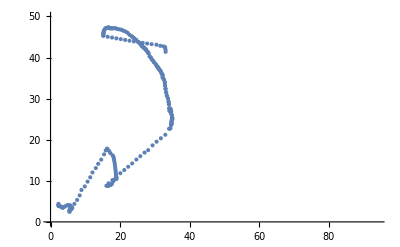
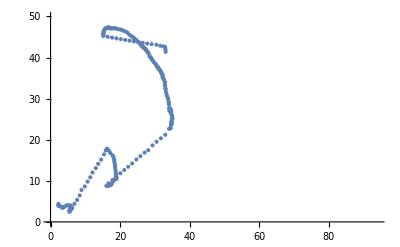
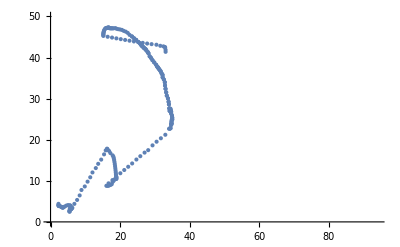
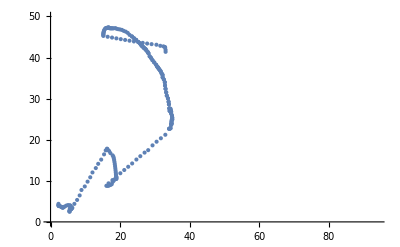
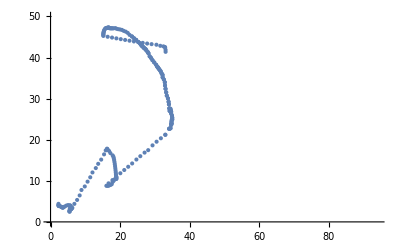
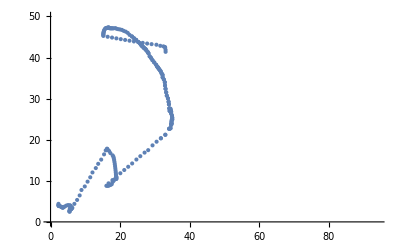
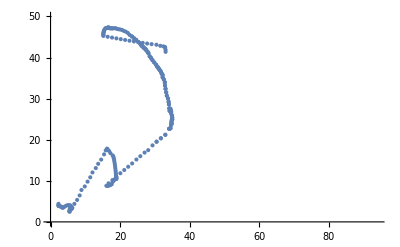
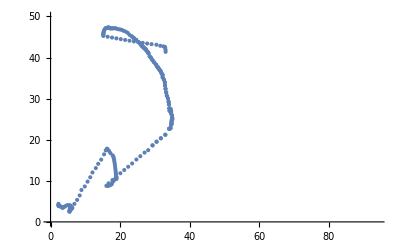

```mathematica
Table[ListPlot[Flatten[ballXY, 1][[;;i]], PlotHighlighting->None, PlotRange->{{0, 94}, {0, 50}}], {i, 250, 260}]
```

```mathematica
Flatten[ballXY, 1][[50;;150]] == Flatten[ballXY, 1][[250;;350]]
```

True

```mathematica
Column[Flatten[ballXY, 1][[50;;75]]]
```

{34.6865,23.6003}
{34.4983,22.7963}
{34.3054,22.7228}
{34.0707,22.6651}
{33.0044,21.2069}
{31.7258,20.3533}
{30.4918,19.5169}
{29.3254,18.6277}
{28.0784,17.4618}
{27.0396,16.8649}
{25.8133,15.989}
{24.6888,15.1832}
{23.4692,14.2248}
{22.3306,13.418}
{21.1972,12.627}
{20.0708,11.8402}
{18.9632,10.8998}
{17.8078,10.1752}
{16.6812,9.38974}
{16.056,8.78516}
{16.4058,8.76333}
{16.7526,8.81312}
{17.2034,8.97574}
{17.5948,9.16468}
{17.8235,9.70086}
{18.1367,10.0058}

```mathematica
Column[Flatten[ballXY, 1][[250;;275]]]
```

{34.6865,23.6003}
{34.4983,22.7963}
{34.3054,22.7228}
{34.0707,22.6651}
{33.0044,21.2069}
{31.7258,20.3533}
{30.4918,19.5169}
{29.3254,18.6277}
{28.0784,17.4618}
{27.0396,16.8649}
{25.8133,15.989}
{24.6888,15.1832}
{23.4692,14.2248}
{22.3306,13.418}
{21.1972,12.627}
{20.0708,11.8402}
{18.9632,10.8998}
{17.8078,10.1752}
{16.6812,9.38974}
{16.056,8.78516}
{16.4058,8.76333}
{16.7526,8.81312}
{17.2034,8.97574}
{17.5948,9.16468}
{17.8235,9.70086}
{18.1367,10.0058}

```mathematica
Length[ballXY[[1]]]
```

150

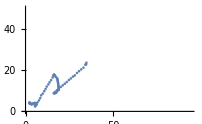

```mathematica
ListPlot[Flatten[ballXY, 1][[50;;150]], PlotHighlighting->None, PlotRange->{{0, 94}, {0, 50}}]
```

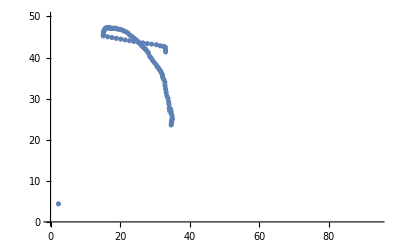

```mathematica
ListPlot[Flatten[ballXY, 1][[150;;250]], PlotHighlighting->None, PlotRange->{{0, 94}, {0, 50}}]
```

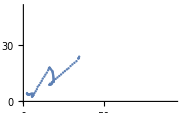

```mathematica
ListPlot[Flatten[ballXY, 1][[250;;350]], PlotHighlighting->None, PlotRange->{{0, 94}, {0, 50}}]
```

```mathematica
Manipulate[
GraphicsColumn[{
ListPlot[Flatten[ballXY, 1][[;;u]], PlotRange->{{-5, 94}, {-5, 50}}, PlotLabel->"Location of Ball"],
ListLinePlot[Flatten[velocities][[;;u]], PlotRange->{{0, 500}, {0, 3}}, PlotLabel->"Speed of Ball"]
}],
{u, 1, 250, 1}]
```

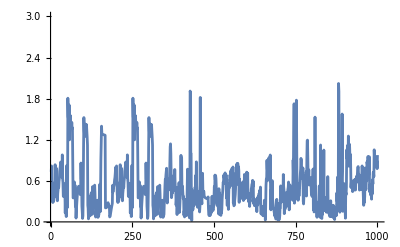

```mathematica
ListLinePlot[Flatten[velocities][[;;1000]], PlotHighlighting->None, PlotRange->3]
```

```mathematica
Mean[Flatten[velocities]]
```

0.504245

## Experimenting

```mathematica
rawData = Import["/Users/erichegonzales/Downloads/01.01.2016.CHA.at.TOR.7z"]
```

```mathematica
emptyEventIdxs = Position[rawData[[3, 2]][[All, 4, 2]], {}]
```

{{33},{34},{55},{56},{57},{80},{81},{82},{83},{84},{85},{86},{89},{109},{110},{111},{126},{150},{151},{152},{153},{154},{155},{156},{187},{188},{201},{202},{213},{214},{215},{229},{230},{246},{247},{294},{452}}

```mathematica
events = Delete[t[[3, 2]], emptyEventIdxs];
```

```mathematica
locs = events[[All, 4, 2, All, 6]];
```

```mathematica
ball = locs[[All, All, 1]];
```

```mathematica
ballXY = ball[[All, All, 3;;4]]
```

```mathematica
Flatten[ballXY, 1]
```

```mathematica
ListPlot[Flatten[ballXY, 1]]
```

```mathematica
ListAnimate[Flatten[ballXY, 1][[;;1000]]]
```

```mathematica
ListLinePlot[Flatten[ballXY, 1][[;;1000]], ColorFunction->Hue]
```

-Graphics-

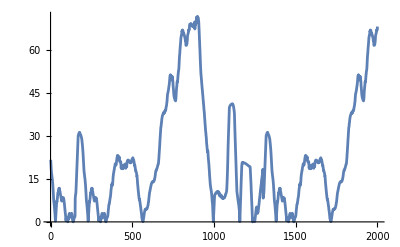

```mathematica
ListLinePlot[velocities[[;;2000]]]
```

```mathematica
events = t[[1]][[3]][[2]][[All, 4, 2]]
```

```mathematica
events =Delete[]
```

```mathematica
ball = t[[1]][[3]][[2]][[All, 4, 2]][[35]]
```

```mathematica
ball = t[[1]][[3]][[2]][[All, 4, 2]][[;;32]][[All, 1, 6, 1]]
```

{{-1,-1,23.4254,45.1273,3.64299},{-1,-1,33.0838,41.3912,5.78885},{-1,-1,33.0838,41.3912,5.78885},{-1,-1,33.0838,41.3912,5.78885},{-1,-1,67.3306,19.3429,3.41494},{-1,-1,10.4277,46.2188,7.88306},{-1,-1,10.4277,46.2188,7.88306},{-1,-1,79.3321,24.8249,3.68148},{-1,-1,22.0857,36.6529,5.86865},{-1,-1,5.07929,27.9458,1.86327},{-1,-1,5.07929,27.9458,1.86327},{-1,-1,80.7198,43.7908,2.19201},{-1,-1,80.7198,43.7908,2.19201},{-1,-1,8.86395,23.5199,4.69182},{-1,-1,8.86395,23.5199,4.69182},{-1,-1,8.86395,23.5199,4.69182},{-1,-1,8.86395,23.5199,4.69182},{-1,-1,8.86395,23.5199,4.69182},{-1,-1,8.86395,23.5199,4.69182},{-1,-1,46.1762,33.6971,2.67256},{-1,-1,35.2783,29.1857,3.87925},{-1,-1,35.2783,29.1857,3.87925},{-1,-1,35.2783,29.1857,3.87925},{-1,-1,15.5048,8.02227,3.14578},{-1,-1,64.5992,32.9382,1.57664},{-1,-1,37.2705,35.4244,4.64446},{-1,-1,68.2009,38.1273,5.16304},{-1,-1,68.2009,38.1273,5.16304},{-1,-1,6.34801,25.0266,10.2466},{-1,-1,6.34801,25.0266,10.2466},{-1,-1,21.6013,38.5198,3.86707},{-1,-1,18.6242,46.2671,2.7233}}

```mathematica
ball[[All, 1, 6, 1]]
```

{{-1,-1,23.4254,45.1273,3.64299},{-1,-1,33.0838,41.3912,5.78885}}

```mathematica
ball[[1]]
```

```mathematica
allEvents =
```

```mathematica
ball2d = ball[[All, 3;;4]];
```

```mathematica
Length[ball2d]
```

150

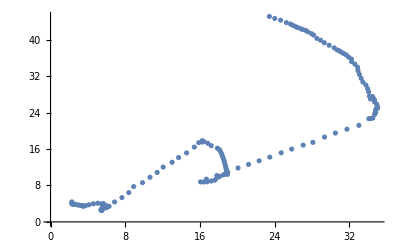

```mathematica
ListPlot[ball2d]
```

```mathematica
t[[1]][[3]][[2]]
```

$Aborted

```mathematica
d1 = t[[1]][[3]][[2]][[3]]
```

```mathematica
Length[d1[[4]][[2]]]
```

1150

make an arrayplot 10x10 with all 0s and Mesh set to True

ArrayPlot[ConstantArray[0, {10, 10}], Mesh -> True]

```mathematica
plot = ArrayPlot[ConstantArray[0, {10, 10}], Mesh -> True];
```

```mathematica
s =d1[[4]][[2]][[All, 6]]
```

```mathematica
b = s[[All, 1]]
```

```mathematica
s
```

{1,1451695250203,713.06,13.04,Null,{{-1,-1,31.5613,42.8569,7.2744},{1610612761,2449,31.8892,23.3014,0.},{1610612761,201960,17.9917,6.50687,0.},{1610612761,200768,11.1841,40.7667,0.},{1610612761,201942,32.7868,42.8549,0.},{1610612761,202685,13.9057,26.3577,0.},{1610612766,101107,22.8872,26.1218,0.},{1610612766,201587,14.6009,11.6591,0.},{1610612766,202689,12.0196,33.9032,0.},{1610612766,203469,13.1932,27.079,0.},{1610612766,203798,29.067,39.5827,0.}}}

```mathematica
coords = s[[All, 3;;4]]
```

{{32.467,42.7215},{32.2035,23.5177},{18.1909,6.40333},{11.0518,40.3191},{32.8065,42.755},{13.698,26.0794},{23.0351,26.1487},{14.733,11.5467},{12.132,33.5081},{13.2499,26.9814},{29.1389,39.5364}}

```mathematica
#/4 & /@coords[[2;;]]
```

{{8.05087,5.87942},{4.54771,1.60083},{2.76296,10.0798},{8.20162,10.6888},{3.42449,6.51985},{5.75877,6.53717},{3.68325,2.88668},{3.03299,8.37703},{3.31248,6.74535},{7.28471,9.88411}}